## Problem 1

## A)

In this part we need to recursively generate the 3rd degree B spline with support [-1,1] and graph it

First, we’ll enter in our data

```mathematica
Clear[tablet]
tablet={-1.0,-.9,-.1,.7,1.0};
```

```mathematica
Clear[b]
```

We’ll now plug in b[0][i] so we can use the recursive relation to find the 3rd degree spline

```mathematica
Do[b[0][i][x_]=Piecewise[{{1,tablet[[i]]≤x<tablet[[i+1]]}}],{i,1,4}
];
```

```mathematica
Definition[b]
```

b[0][1][x_]=Piecewise[{{1, -1.≤x<-0.9}, {0, True}}]
 
b[0][2][x_]=Piecewise[{{1, -0.9≤x<-0.1}, {0, True}}]
 
b[0][3][x_]=Piecewise[{{1, -0.1≤x<0.7}, {0, True}}]
 
b[0][4][x_]=Piecewise[{{1, 0.7≤x<1.}, {0, True}}]

```mathematica
t=tablet
```

{-1.,-0.9,-0.1,0.7,1.}

```mathematica
Clear[i];
Clear[k];
Clear[x];
```

Now that we have this we can implement a for loop that will find us up to the third degree spline.

```mathematica
For[k=1,k<4,k++,
For[i=1,i<5-k,i++,
b[k][i][x_]=(x-t[[i]])/(t[[i+k]]-t[[i]])*b[k-1][i][x]+(t[[i+k+1]]-x)/(t[[i+k+1]]-t[[i+1]])*b[k-1][i+1][x]]] (*This is the recursive relation defined in the book*)
```

```mathematica
Definition[b];
```

So now that we have coded and ran the result, we can get our answer by simplifying b[3][1][x] (note B[3][1] is the same as B_0^3(x) since our data points are indexed at 1).

```mathematica
Simplify[b[3][1][x]]
```

Piecewise[{{0., x≥1.||x<-1.}, {-1.5949 (-1.+1. x)^3, 0.7≤x<1.}, {6.53595 (1.+1. x)^3, -1.≤x<-0.9}, {0.544038-0.281013 x-1.64913 x^2+1.46883 x^3, -0.1≤x<0.7}, {0.540882-0.375709 x-2.5961 x^2-1.68774 x^3, True}}]

So B_0^3(x)=Piecewise[{{0., x≥1.||x<-1.}, {-1.5949 (-1+1 x)^3, 0.7≤x<1.}, {6.53595 (1+1 x)^3, -1.≤x<-0.9}, {0.544038-0.281013 x-1.64913 x^2+1.46883 x^3, -0.1≤x<0.7}, {0.540882-0.375709 x-2.5961 x^2-1.68774 x^3, -0.9≤x<-0.1}}]

Now we plot it

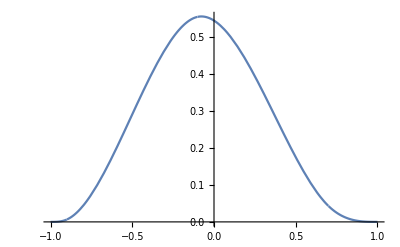

```mathematica
Plot[b[3][1][x],{x,-1,1}]
```

## B)

In this part we need to take the derivative of (B^3)_0(x) using Mathematica and check that it is continuous 

So we’ll first take the derivative of B_0^3(x)

```mathematica
Simplify[D[b[3][1][x],x]]
```

Piecewise[{{0., x>1||x<-1.}, {-0.375709-5.19221 x-5.06321 x^2, -9/10<x<-1/10}, {-4.78469 (1.-1. x)^2, 7/10<x<1}, {-0.281013-3.29827 x+4.40649 x^2, -1/10<x<7/10}, {19.6078 (1.+1. x)^2, -1.<x<-0.9}, {Indeterminate, True}}]

```mathematica
derivativeform=(3/(t[[4]]-t[[1]]))*b[2][1][x]-(3/(t[[5]]-t[[2]]))(b[2][2][x]);
```

```mathematica
derivative[x_]=derivativeform;
```

```mathematica
Simplify[derivative[x]]
```

Piecewise[{{0., x≥1.||x<-1.}, {19.6078 (1.+1. x)^2, -1.≤x<-0.9}, {-0.375709-5.19221 x-5.06321 x^2, -0.9≤x<-0.1}, {-4.78469 (1.-1. x)^2, 0.7≤x<1.}, {-0.281013-3.29827 x+4.40649 x^2, True}}]

(The above piecewise function is what you would get if you use the formula given in the book for the derivatives)

So our derivative is

Piecewise[{{0., x≥1.||x<-1.}, {19.6078 (1.+1. x)^2, -1.≤x<-0.9}, {-0.375709-5.19221 x-5.06321 x^2, -0.9≤x<-0.1}, {-4.78469 (1.-1. x)^2, 0.7≤x<1.}, {-0.281013-3.29827 x+4.40649 x^2, -0.1≤x<0.7}}]

To check if this is continuous, we need to check to see if lim_(x→t_i^-) b'_0^3(x)=lim_(x→t_i^+) b'_0^3(x) 
(Note: For some reason Mathematica get’s rid of the t_i≤x<t_(i+1) and makes it t_i<x<t_(i+1)  when taking the derivative and I don’t know how to fix that, but I checked the result is the same when using the derivative formula in the book and it is). The formatting for this is gonna be rough, but here we go (I’ll just copy and paste from our integral from above and the limit approaching the left hand side or lim_(x→t_i^-) b'_0^3(x) will be copied in first)

For lim_(x→-(.9)^-) b'_0^3(x)  and  lim_(x→-.9) b'_0^3(x):

```mathematica
19.60784313725491 (1.+1. *-.9)^2
```

0.196078

```mathematica
-0.3757094943240454-5.192208462332301 *-.9-5.063209494324045 *(.9)^2
```

0.196078

So lim_(x→-(.9)^-) b'_0^3(x) =lim_(x→-.9) b'_0^3(x), so we’re good for this limit

For lim_(x→-(.1)^-) b'_0^3(x)  and  lim_(x→-.1) b'_0^3(x):

```mathematica
-0.3757094943240454-5.192208462332301 *(-.1)-5.063209494324045 *(-.1)^2
```

0.0928793

```mathematica
-0.28101252462707577-3.298269068392907 *-.1+4.4064874753729235 *(-.1)^2
```

0.0928793

Solim_(x→-(.1)^-) b'_0^3(x) =lim_(x→-.1) b'_0^3(x),so we're good for this limit

Lastly we have to check  lim_(x→(.7)^-) b'_0^3(x)  and  lim_(x→.7) b'_0^3(x):

```mathematica
-0.28101252462707577-3.298269068392907 *.7+4.4064874753729235 *(.7)^2
```

-0.430622

```mathematica
-4.78468899521531 (1.-1. *.7)^2
```

-0.430622

So we’re good here as well which means are derivative is continuous since we’re continuous across all t_i and all intervals in our piecwise functions are continuous

## C)

```mathematica
Simplify[D[derivative[x],x]]
```

Piecewise[{{0., x>1||x<-1.}, {-5.19221-10.1264 x, -9/10<x<-1/10}, {9.56938-9.56938 x, 7/10<x<1}, {-3.29827+8.81297 x, -1/10<x<7/10}, {39.2157+39.2157 x, -1.<x<-0.9}, {Indeterminate, True}}]

```mathematica
secondderiv=Piecewise[{{0, x>1||x<-1},{-5.192208462332301-10.126418988648092 x,-.9≤x<-.1},{9.56937799043062-9.56937799043062 x,.7≤x<1},{-3.2982690683929077+8.812974950745849 x,-.1≤x<.7},{39.215686274509814+39.215686274509814 x,-1≤x<-.9}}]
```

Piecewise[{{0, x>1||x<-1}, {-5.19221-10.1264 x, -0.9≤x<-0.1}, {9.56938-9.56938 x, 0.7≤x<1}, {-3.29827+8.81297 x, -0.1≤x<0.7}, {39.2157+39.2157 x, -1≤x<-0.9}, {0, True}}]

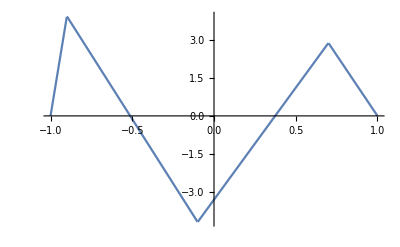

```mathematica
Plot[secondderiv,{x,-1,1}]
```

So the second derivative of B_0^3(x) looks continuous from our graph, although it might not be differentiable at -.9,-.1, and .7.

## Problem 2

```mathematica
tablex=Table[.2i,{i,0,10}]
tabley={0.30567044593433224,0.4063255538032995,0.7529553318223484,0.29379611325014754,0.8583835668031451,0.7456943493696915,1.4463622238223015,1.887107733671204,2.0687411826279494,2.8375245432939282,3.4993238876193593}
data=Table[{tablex[[i]],tabley[[i]]},{i,11}]
```

{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.}

{0.30567,0.406326,0.752955,0.293796,0.858384,0.745694,1.44636,1.88711,2.06874,2.83752,3.49932}

{{0.,0.30567},{0.2,0.406326},{0.4,0.752955},{0.6,0.293796},{0.8,0.858384},{1.,0.745694},{1.2,1.44636},{1.4,1.88711},{1.6,2.06874},{1.8,2.83752},{2.,3.49932}}

## A)

In this part we need to set up a matrix equation using the transpose method to construct a model of the form r(x)=a+bx+ce^x that fits the data {{0.,0.30567},{0.2,0.406326},{0.4,0.752955},{0.6,0.293796},{0.8,0.858384},{1.,0.745694},{1.2,1.44636},{1.4,1.88711},{1.6,2.06874},{1.8,2.83752},{2.,3.49932}}
So we’ll start by plugging in our x-values into the equation and separate each coefficient unknown into a matrix

```mathematica
mx=Table[{1,tablex[[i]],Exp[tablex[[i]]]},{i,11}]
```

{{1,0.,1.},{1,0.2,1.2214},{1,0.4,1.49182},{1,0.6,1.82212},{1,0.8,2.22554},{1,1.,2.71828},{1,1.2,3.32012},{1,1.4,4.0552},{1,1.6,4.95303},{1,1.8,6.04965},{1,2.,7.38906}}

```mathematica
matrix =Join[Transpose[mx].mx,Transpose[{Transpose[mx].tabley}],2]
```

{{11.,11.,36.2462,15.1019},{11.,15.4,49.6867,21.7849},{36.2462,49.6867,163.576,72.1219}}

```mathematica
MatrixForm[matrix]
```

(11. | 11. | 36.2462 | 15.1019
11. | 15.4 | 49.6867 | 21.7849
36.2462 | 49.6867 | 163.576 | 72.1219)

So this is the matrix equation we need to solve and we can now do this by using linear solve and this will give us our coefficients a,b,c (each column corresponds to a different coefficient)

```mathematica
{a,b,c}=LinearSolve[Transpose[mx].mx,Transpose[mx].tabley]
```

{-0.297589,-0.407375,0.63059}

Now that we have our coefficients we can get our regression equation.

```mathematica
reg[x_]:=a+b*x+c*Exp[x]
```

```mathematica
reg[x]
```

-0.297589+0.63059 ⅇ^x-0.407375 x

This is our fitted equation for the data given the form r(x)=a+bx+ce^x

## B)

In this problem we need to plot reg[x] and our points on the same graph

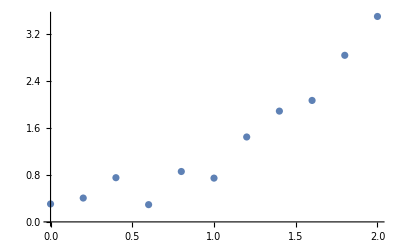

```mathematica
dotgraph=ListPlot[data]
```

```mathematica
reggraph=Plot[reg[x],{x,0,2}];
```

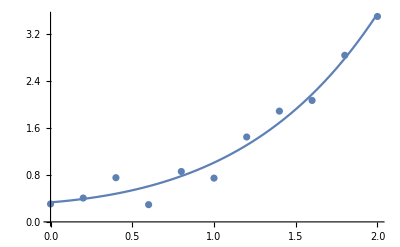

```mathematica
Show[dotgraph,reggraph]
```

Our graph is looking very nice which means we can move onto the next part

## C).

In this part we need to find the sum of squared differences between the y-values and the values predicted by our model.

So the equation for this will look something like (∑_1)^npoints(y value -predicted y (value))^2

```mathematica
Sum[(tabley[[i]]-reg[tablex[[i]]])^2,{i,11}]
```

0.323775

So the sum of squared differences between the y-values and the values predicted by our model is about 0.323775

## D).

We now need to repeat the above steps for t(x)=a+bx^2+ce^x

First we’ll set up the matrix equation

```mathematica
mx1=Table[{1,tablex[[i]]^2,Exp[tablex[[i]]]},{i,11}]
```

{{1,0.,1.},{1,0.04,1.2214},{1,0.16,1.49182},{1,0.36,1.82212},{1,0.64,2.22554},{1,1.,2.71828},{1,1.44,3.32012},{1,1.96,4.0552},{1,2.56,4.95303},{1,3.24,6.04965},{1,4.,7.38906}}

```mathematica
matrix1 =Join[Transpose[mx1].mx1,Transpose[{Transpose[mx1].tabley}],2]
```

{{11.,15.4,36.2462,15.1019},{15.4,40.5328,79.6521,35.8059},{36.2462,79.6521,163.576,72.1219}}

```mathematica
MatrixForm[matrix1]
```

(11. | 15.4 | 36.2462 | 15.1019
15.4 | 40.5328 | 79.6521 | 35.8059
36.2462 | 79.6521 | 163.576 | 72.1219)

So this is the matrix equation we need to solve to find a, b, and c and we can easily do that using linear solve

```mathematica
{a,b,c}=LinearSolve[Transpose[mx1].mx1,Transpose[mx1].tabley]
```

{0.0726049,0.486637,0.187855}

So now that we have solved for our coefficients we can get our regression equation which is

```mathematica
Clear[t]
```

```mathematica
t[x_]=a+b*x^2+c*Exp[x]
```

0.0726049+0.187855 ⅇ^x+0.486637 x^2

Now that we have this function we can plot it on the same graph

```mathematica
graphreg2=Plot[t[x],{x,0,2}];
```

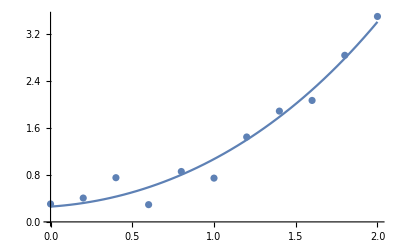

```mathematica
Show[dotgraph,graphreg2]
```

Now that we’ve graphed this we can find the sum of squared differences between the y-values and the values predicted by our model

```mathematica
Sum[(tabley[[i]]-t[tablex[[i]]])^2,{i,11}]
```

0.364941

So the sum of squared differences between the y-values and the values predicted by our model l is about 0.364941

So based off the variance it looks like the first model is a slightly better fit for the graph since it has less noise than the second fit.

So

```mathematica
reg[x]
```

0.0726049+0.187855 ⅇ^x+0.486637 x

is the better model.

## Problem 3

We need to start of by construction a data table that has 10 evenly spaced x-values on the interval [-1,1] and generate y-values using the function y=e^x

```mathematica
datax=Table[-1+i(2/9),{i,0,9}]
```

{-1,-7/9,-5/9,-1/3,-1/9,1/9,1/3,5/9,7/9,1}

```mathematica
datay=Table[Exp[datax[[i]]],{i,1,10}]
```

{1/ⅇ,1/ⅇ^(7/9),1/ⅇ^(5/9),1/ⅇ^(1/3),1/ⅇ^(1/9),ⅇ^(1/9),ⅇ^(1/3),ⅇ^(5/9),ⅇ^(7/9),ⅇ}

## A)

We now need to recursively generate the first 5 Chebyshev polynomials and we know that T_0(x)=1 and T_1(x)=x, so we can now use the recursive relation T_j(x)=2xT_(j-1)(x)-T_(j-2)(x). So we’ll code this up in mathematica.

```mathematica
Clear[t]
```

```mathematica
t[0][x_]=1
```

1

```mathematica
t[1][x_]=x
```

x

```mathematica
Do[t[i][x_]=2x*t[i-1][x]-t[i-2][x],{i,2,4}](*This is the recursive relation *)
```

```mathematica
For[i=0,i<5,i++,
Print["t[",i,"][x]= ",Expand[t[i][x]]]]
```

t[0][x]= 1

t[1][x]= x

t[2][x]= -1+2 x^2

t[3][x]= -3 x+4 x^3

t[4][x]= 1-8 x^2+8 x^4

So these are the first five Chebyshev polynomials

## B)

```mathematica
t[2]
```

t[2]

```mathematica
t[2][3]
```

17

```mathematica
t[4][3]
```

577

In this part we need to use the Chebyshev polynomials we just found to find a 4th degree polynomial model to fit the data using a similar matrix equation we used in the previous problem, so we need to find aT_0(x)+bT_1(x)+cT_2(x)+....  We also need to express this polynomial as a linear combination of the Chebyshev polynomials and simplify it into the standard form of a polynomial.

We first create a matrix that puts all the different data point values evaluated at x in different rows for each datax

```mathematica
cheby4=Table[Table[t[i][datax[[j]]],{i,0,4}],{j,10}];
```

```mathematica
MatrixForm[cheby4]
```

(1 | -1 | 1 | -1 | 1
1 | -7/9 | 17/81 | 329/729 | -5983/6561
1 | -5/9 | -31/81 | 715/729 | -4639/6561
1 | -1/3 | -7/9 | 23/27 | 17/81
1 | -1/9 | -79/81 | 239/729 | 5921/6561
1 | 1/9 | -79/81 | -239/729 | 5921/6561
1 | 1/3 | -7/9 | -23/27 | 17/81
1 | 5/9 | -31/81 | -715/729 | -4639/6561
1 | 7/9 | 17/81 | -329/729 | -5983/6561
1 | 1 | 1 | 1 | 1)

Now we can set up our matrix equation and solve this using linear solve

```mathematica
cheby4sol=N[LinearSolve[Transpose[cheby4].cheby4,Transpose[cheby4].datay]]
```

{1.26608,1.13052,0.271515,0.0443939,0.00547599}

```mathematica
reg4[x_]=Sum[cheby4sol[[i+1]]*t[i][x],{i,0,4}]
```

1.26608+1.13052 x+0.271515 (-1+2 x^2)+0.0443939 (-x+2 x (-1+2 x^2))+0.00547599 (1-2 x^2+2 x (-x+2 x (-1+2 x^2)))

So the above solution is expressed as a linear combination of all the Chebyshev polynomials. Now we need to simplify this to express it as a normal polynomial, and we can do this by simplifying the solution:

```mathematica
Simplify[reg4[x]]
```

1.00004+0.997343 x+0.499222 x^2+0.177576 x^3+0.0438079 x^4

So this is our polynomial in the normal form.

## C)

We now need to graph reg4[x] on the same graph as the data points 

First we plot the original data points

```mathematica
data2=Table[{datax[[i]],datay[[i]]},{i,10}];
```

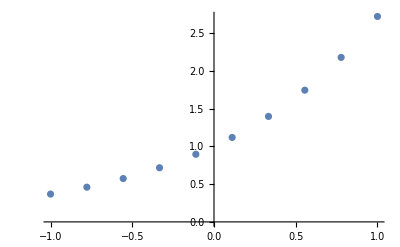

```mathematica
pointplot=ListPlot[data2]
```

Now we plot the regression graph

```mathematica
reg4graph=Plot[reg4[x],{x,-1,1}];
```

Together they look like

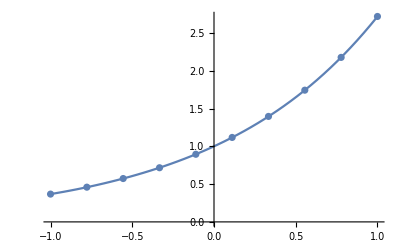

```mathematica
Show[pointplot,reg4graph]
```

So it looks like we got a very good solution based off our graph.

## D)

In this part we need to determine which of the data points is farthest from the curve and by how much. We can find this by subtracting the following equation max(√(yvalue-reg4(x_(at y value)))^2) for all the data points we have, so we now will implement this in Mathematica.

```mathematica
distances={};
```

```mathematica
For[i=1,i<11,i++,
AppendTo[distances,Sqrt[(datay[[i]]-reg4[datax[[i]]])^2]]]
```

```mathematica
distances
```

{0.000271144,0.000618393,0.0000119751,0.00049346,0.000310509,0.000250264,0.000538495,0.0000876003,0.000701453,0.000293789}

So we now have all the distances for the corresponding data values, we can now find the max easily using Mathematica

```mathematica
Max[distances]
```

0.000701453

So the max happens at the 9th data point which is

```mathematica
data2[[9]]
```

{7/9,ⅇ^(7/9)}

and it has a distance of approximately 0.000701453 from the curve.

## Problem 4

In this problem we need to estimate the value of ∫_C zdC where C is the cylinder determined by x^2+y^2≤1 and 1≤z≤3 and we’re supposed to use 500 points. We can start off by seeing that this cylinder has a radius of R=1 and a height of 2, so it’s volume is π1^2*2=2π. Now that we have this we code the rest of it up

```mathematica
monteintegral[npoints_]:=Module[{sum,avg1,vol1,x,y,z,coeff},
x=RandomReal[{-1,1},npoints];
coeff=RandomChoice[{-1,1},npoints];(*This will make something randomly postive/negative *)
y=Do[coeff[[i]]*RandomReal[{0,Sqrt[1-x[[i]]^2]}],{i,npoints}];(* We know y≤1-x^2 so we can choose random between {0, the max y can be} and it will randomly make is positive or negative*)
z=RandomReal[{1,3},npoints];
sum=0;
For[i=1,i<npoints+1,i++,
sum+= z[[i]]];
avg1=sum/npoints;(*avg value of all of z inside the cylinder *)
vol1=avg1*2Pi;(* we have a cylinder of volume 2 π1^2*)
Return[vol1]]
```

```mathematica
monteintegral[500]
```

12.574

So when we do this with 500 points we’re getting around a volume of 12.574

## Problem 5

In this problem we need to generate 1000 [points in the square [-1,1]x[1,1] and find the proportion of them that lie in the unit circle to give an estimate of π. We can use the fact that we know the area of rectangle is 4 and multiple this by the ratio of points we find in the unit circle to give us the estimate of pi

First we generate 1000 random points in the square and then write the rest of the code that does this.

```mathematica
points=RandomReal[{-1,1},{1000,2}];

approxpi[points_]:=Module[{incircle,totalpoints,x,y,estimation,ratio},
incircle=0; (*number of points from randomly generated points that lie in the unit circle *)
totalpoints=Length[points];
For[i=1,i<Length[points]+1,i++,
x=points[[i]][[1]];
y=points[[i]][[2]];(*Corresponds to x and y data points *)
If[x^2+y^2≤1,incircle+=1]];(*Checks to see if our points are inside the unit circle *)
ratio=incircle/totalpoints;(*divides the total number of points in the unit circle by 1000 *)
estimation=4*ratio;(*Multiplies the ratio of points inside the unit circle by the area of the square *)
Return[N[estimation]]]
```

So we can now approximate pi using the code we have written and we get it to be about

```mathematica
approxpi[points]
```

3.12

This is looks like it’s getting around pi which means everything is working nicely.